## Differences between primes

```mathematica
results={};
n=7;primes=allPrimes[[n]];
```

## Prime 7

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
(* Removed first, 2 -> 3, the only transition with d = 1 *)
```

```mathematica
diffs=diffs[[;;500]];
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igv7=Graph[visibles, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv7];
```

```mathematica
count = Total[adj]//Counts
```

<|60→5,59→2,61→2,62→2,63→2,64→2,65→2,70→1,71→1,73→1,66→1,76→2,74→1,80→1,78→2,89→2,92→1,75→1,90→1,53→2,94→2,115→1,99→1,114→1,107→1,85→1,130→1,128→1,124→1,149→1,155→1,166→1,159→1,204→1,171→1,196→1,185→1,210→1,191→1,227→1,224→1,250→1,245→1,301→1,292→1,311→1,56→1,52→2,47→2,49→1,46→2,43→2,45→1,42→2,41→1,37→5,40→2,44→2,34→1,31→2,38→1,36→4,28→6,35→2,33→1,29→3,30→1,27→4,24→4,26→7,22→7,19→8,25→7,21→9,20→7,15→14,18→8,32→1,23→6,17→8,12→12,14→11,11→15,9→17,13→10,16→6,7→24,8→22,6→31,5→23,10→12,3→45,4→42,2→34,1→1|>

```mathematica
count=count[[;;-2]]
```

<|60→5,59→2,61→2,62→2,63→2,64→2,65→2,70→1,71→1,73→1,66→1,76→2,74→1,80→1,78→2,89→2,92→1,75→1,90→1,53→2,94→2,115→1,99→1,114→1,107→1,85→1,130→1,128→1,124→1,149→1,155→1,166→1,159→1,204→1,171→1,196→1,185→1,210→1,191→1,227→1,224→1,250→1,245→1,301→1,292→1,311→1,56→1,52→2,47→2,49→1,46→2,43→2,45→1,42→2,41→1,37→5,40→2,44→2,34→1,31→2,38→1,36→4,28→6,35→2,33→1,29→3,30→1,27→4,24→4,26→7,22→7,19→8,25→7,21→9,20→7,15→14,18→8,32→1,23→6,17→8,12→12,14→11,11→15,9→17,13→10,16→6,7→24,8→22,6→31,5→23,10→12,3→45,4→42,2→34|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{60,1/100},{59,1/250},{61,1/250},{62,1/250},{63,1/250},{64,1/250},{65,1/250},{70,1/500},{71,1/500},{73,1/500},{66,1/500},{76,1/250},{74,1/500},{80,1/500},{78,1/250},{89,1/250},{92,1/500},{75,1/500},{90,1/500},{53,1/250},{94,1/250},{115,1/500},{99,1/500},{114,1/500},{107,1/500},{85,1/500},{130,1/500},{128,1/500},{124,1/500},{149,1/500},{155,1/500},{166,1/500},{159,1/500},{204,1/500},{171,1/500},{196,1/500},{185,1/500},{210,1/500},{191,1/500},{227,1/500},{224,1/500},{250,1/500},{245,1/500},{301,1/500},{292,1/500},{311,1/500},{56,1/500},{52,1/250},{47,1/250},{49,1/500},{46,1/250},{43,1/250},{45,1/500},{42,1/250},{41,1/500},{37,1/100},{40,1/250},{44,1/250},{34,1/500},{31,1/250},{38,1/500},{36,1/125},{28,3/250},{35,1/250},{33,1/500},{29,3/500},{30,1/500},{27,1/125},{24,1/125},{26,7/500},{22,7/500},{19,2/125},{25,7/500},{21,9/500},{20,7/500},{15,7/250},{18,2/125},{32,1/500},{23,3/250},{17,2/125},{12,3/125},{14,11/500},{11,3/100},{9,17/500},{13,1/50},{16,3/250},{7,6/125},{8,11/250},{6,31/500},{5,23/500},{10,3/125},{3,9/100},{4,21/250},{2,17/250}}

```mathematica
countrel = countrel[[2;;]]
```

{{61,1/250},{62,1/250},{63,1/250},{64,1/250},{65,1/250},{70,1/500},{71,1/500},{73,1/500},{66,1/500},{76,1/250},{74,1/500},{80,1/500},{78,1/250},{89,1/250},{92,1/500},{75,1/500},{90,1/500},{53,1/250},{94,1/250},{115,1/500},{99,1/500},{114,1/500},{107,1/500},{85,1/500},{130,1/500},{128,1/500},{124,1/500},{149,1/500},{155,1/500},{166,1/500},{159,1/500},{204,1/500},{171,1/500},{196,1/500},{185,1/500},{210,1/500},{191,1/500},{227,1/500},{224,1/500},{250,1/500},{245,1/500},{301,1/500},{292,1/500},{311,1/500},{56,1/500},{52,1/250},{47,1/250},{49,1/500},{46,1/250},{43,1/250},{45,1/500},{42,1/250},{41,1/500},{37,1/100},{40,1/250},{44,1/250},{34,1/500},{31,1/250},{38,1/500},{36,1/125},{28,3/250},{35,1/250},{33,1/500},{29,3/500},{30,1/500},{27,1/125},{24,1/125},{26,7/500},{22,7/500},{19,2/125},{25,7/500},{21,9/500},{20,7/500},{15,7/250},{18,2/125},{32,1/500},{23,3/250},{17,2/125},{12,3/125},{14,11/500},{11,3/100},{9,17/500},{13,1/50},{16,3/250},{7,6/125},{8,11/250},{6,31/500},{5,23/500},{10,3/125},{3,9/100},{4,21/250},{2,17/250},{1,1/500}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.179495/x^0.825677]

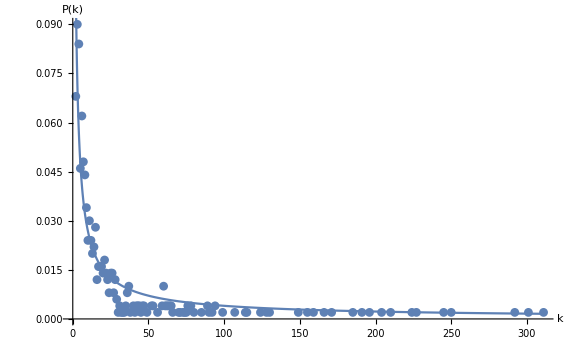

```mathematica
vis7=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-7.eps",vis7];
```

## Mean degree

```mathematica
degree=VertexDegree[igv7]//Mean//N
```

25.124

```mathematica
Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]
```

{visibility,7,500,25.124,0.825677 ± 0.0725238,0.179495 ± 0.0247785}

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igh7=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh7];
```

```mathematica
count = Total[adj]//Counts
```

<|1→1,2→3359,3→2223,4→1541,5→943,6→643,7→422,8→277,9→205,11→86,10→136,14→30,12→60,13→44,15→13,16→6,17→5,19→2,20→1,24→1,18→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

```mathematica
countrel={{2,3359/9999},{3,247/1111},{4,1541/9999},{5,943/9999},{6,643/9999},{7,422/9999},{8,277/9999},{9,205/9999},{11,86/9999},{10,136/9999},{14,10/3333},{12,20/3333},{13,4/909},{15,13/9999},{16,2/3333},{17,5/9999},{19,2/9999},{20,1/9999},{24,1/9999},{18,1/9999}}
```

{{2,3359/9999},{3,247/1111},{4,1541/9999},{5,943/9999},{6,643/9999},{7,422/9999},{8,277/9999},{9,205/9999},{11,86/9999},{10,136/9999},{14,10/3333},{12,20/3333},{13,4/909},{15,13/9999},{16,2/3333},{17,5/9999},{19,2/9999},{20,1/9999},{24,1/9999},{18,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

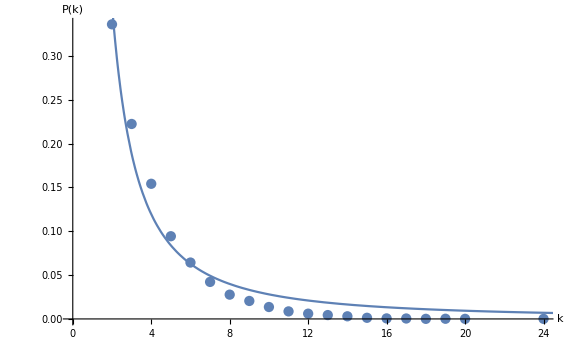

```mathematica
hvis7=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-7.eps",hvis7];
```

## Mean degree

```mathematica
degree=VertexDegree[igh7]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,2,9999,6.16702,1.08261 ± 0.173904,0.380813 ± 0.100447},{horizontal,2,9999,3.66877,1.6666 ± 0.250868,1.22997 ± 0.303261},{visibility,3,9999,6.52165,1.07386 ± 0.17242,0.413716 ± 0.104511},{horizontal,3,9999,3.9846,1.58206 ± 0.196895,1.06966 ± 0.215147},{visibility,4,9999,6.39604,1.56878 ± 0.133599,1.21001 ± 0.239174},{horizontal,4,9999,3.47475,1.93054 ± 0.154407,1.67857 ± 0.234004},{visibility,5,9999,14.2592,1.53624 ± 0.047473,1.02742 ± 0.0732728},{horizontal,5,9999,3.9728,1.58228 ± 0.197018,1.07061 ± 0.215454},{visibility,6,9999,6.33003,1.08581 ± 0.174458,0.425596 ± 0.107304},{horizontal,6,9999,3.88559,1.62075 ± 0.196107,1.1307 ± 0.222727},{visibility,7,9999,27.6872,1.01419 ± 0.0648361,0.285856 ± 0.0302598},{horizontal,7,9999,3.9638,1.58278 ± 0.197671,1.07175 ± 0.216374}}